# Runtime Testing

```mathematica
<<StoChemSim`
```

## Direct SSA

All system constructions have number of reactions = number of species.

```mathematica
(*System 1: Every species appears in precisely 1 reaction. Every reaction has only 1 reactant and 1 product.*)
ConstructSys1[n_]:=Module[
{rxns,xConcs,yConcs,concs},
rxns= Table[revrxn[x[i],y[i],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xConcs=Table[conc[x[i],RandomInteger[100]],{i,n}];
yConcs=Table[conc[y[i],RandomInteger[100]],{i,n}];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
(*System 2: Every species appears in O(sqrt(n)) reactions. Every reaction has O(sqrt(n)) reactants and O(sqrt(n)) products.*)
ConstructSys2[n_]:=Module[
{k,rxns,xConcs,yConcs,concs},
k=Round[Sqrt[n]];
rxns= Flatten[Table[revrxn[Plus@@Table[x[i,l]+x[j,l],{l,k}],Plus@@Table[y[i,l]+y[j,l],{l,k}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,k},{j,k}]];
xConcs=Flatten[Table[conc[x[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
yConcs=Flatten[Table[conc[y[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
(*System 3: Every species appears in all reactions. Every reaction has O(n) reactants and O(n) products.*)
ConstructSys3[n_]:=Module[
{rxns,xConcs,yConcs,concs},
rxns= Table[revrxn[Plus@@Table[x[j],{j,n}],Plus@@Table[y[j],{j,n}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xConcs=Table[conc[x[i],RandomInteger[100]],{i,n}];
yConcs=Table[conc[y[i],RandomInteger[100]],{i,n}];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
TestSysSSA[construction_,kRange_,iters_,statesOnlyFlag_]:=Module[{},
Table[Module[
{n,rxns,concs,rxnsys,nRxns,nSpecies,results,totalTime,runtimeInfo,timePerIter,algoTimePerIter,out},
n=k^2;
{rxns,concs} = construction[n];
rxnsys=Flatten[{rxns,concs}];
nRxns=Length[ExpandRevrxns[rxns]];
nSpecies=Length[SpeciesInRxnsys[rxnsys]];
results=Timing[SimulateDirectSSA[rxnsys,useIter->True,iterEnd->iters,statesOnly->statesOnlyFlag,finalOnly->True,outputTS->False]];
totalTime=results[[1]];
runtimeInfo=GetRuntimeInfo[];
timePerIter=runtimeInfo["backend algorithm"]/iters;
out={construction,statesOnlyFlag,nRxns,nSpecies,iters,totalTime,timePerIter,runtimeInfo};
Print[out];
out],
{k,kRange}]]
```

## Constructions 1, 2, and 3 up to 200 reactions

```mathematica
constructions={ConstructSys1,ConstructSys2,ConstructSys3};
kRange={1,3,5,10};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA=Table[TestSysSSA[constructions[[i]],kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.109375,1.17552×10^-6,<|frontend→0.,interface→7.7×10^-6,backend→0.117552|>}

{ConstructSys1,False,18,18,100000,0.28125,2.75182×10^-6,<|frontend→0.,interface→0.0000272,backend→0.275182|>}

{ConstructSys1,False,50,50,100000,0.515625,5.2562×10^-6,<|frontend→0.,interface→0.0000702,backend→0.52562|>}

{ConstructSys1,False,200,200,100000,1.625,0.000015983,<|frontend→0.03125,interface→0.0006949,backend→1.5983|>}

{ConstructSys1,True,2,2,100000,0.109375,1.07203×10^-6,<|frontend→0.,interface→5.6×10^-6,backend→0.107203|>}

{ConstructSys1,True,18,18,100000,0.25,2.44651×10^-6,<|frontend→0.,interface→0.0000207,backend→0.244651|>}

{ConstructSys1,True,50,50,100000,0.515625,5.28888×10^-6,<|frontend→0.,interface→0.0000731,backend→0.528888|>}

{ConstructSys1,True,200,200,100000,1.625,0.0000159452,<|frontend→0.03125,interface→0.0003427,backend→1.59452|>}

{ConstructSys2,False,2,2,100000,0.109375,1.1391×10^-6,<|frontend→0.,interface→4.7×10^-6,backend→0.11391|>}

{ConstructSys2,False,18,18,100000,0.65625,6.44249×10^-6,<|frontend→0.,interface→0.0000862,backend→0.644249|>}

{ConstructSys2,False,50,50,100000,1.4375,0.0000143023,<|frontend→0.015625,interface→0.0001797,backend→1.43023|>}

{ConstructSys2,False,200,200,100000,4.70313,0.0000462955,<|frontend→0.0625,interface→0.0021687,backend→4.62955|>}

{ConstructSys2,True,2,2,100000,0.109375,1.16247×10^-6,<|frontend→0.,interface→8.4×10^-6,backend→0.116247|>}

{ConstructSys2,True,18,18,100000,0.625,6.29689×10^-6,<|frontend→0.015625,interface→0.0000606,backend→0.629689|>}

{ConstructSys2,True,50,50,100000,1.35938,0.0000133793,<|frontend→0.015625,interface→0.0002264,backend→1.33793|>}

{ConstructSys2,True,200,200,100000,4.89063,0.0000486674,<|frontend→0.0625,interface→0.0004212,backend→4.86674|>}

{ConstructSys3,False,2,2,100000,0.125,1.11111×10^-6,<|frontend→0.,interface→6.8×10^-6,backend→0.111111|>}

{ConstructSys3,False,18,18,100000,0.796875,8.09918×10^-6,<|frontend→0.,interface→0.0000391,backend→0.809918|>}

{ConstructSys3,False,50,50,100000,2.53125,0.0000249919,<|frontend→0.03125,interface→0.0009806,backend→2.49919|>}

{ConstructSys3,False,200,200,100000,17.,0.000168033,<|frontend→0.21875,interface→0.0030019,backend→16.8033|>}

{ConstructSys3,True,2,2,100000,0.109375,1.03804×10^-6,<|frontend→0.,interface→6.2×10^-6,backend→0.103804|>}

{ConstructSys3,True,18,18,100000,0.796875,7.85136×10^-6,<|frontend→0.,interface→0.0000384,backend→0.785136|>}

{ConstructSys3,True,50,50,100000,2.92188,0.0000293018,<|frontend→0.015625,interface→0.0002792,backend→2.93018|>}

{ConstructSys3,True,200,200,100000,0.21875,5.5162×10^-8,<|frontend→0.203125,interface→0.0017009,backend→0.0055162|>}

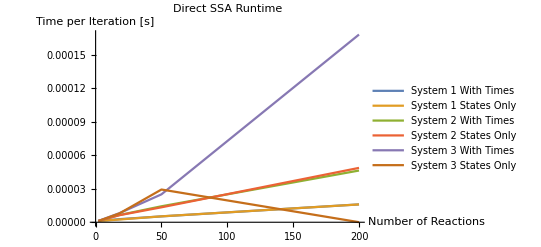

```mathematica
coorsSSA=Flatten[Table[
Table[{resultsSSA[[i]][[j]][[l]][[3]],resultsSSA[[i]][[j]][[l]][[7]]},{l,Length[resultsSSA[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1","System 2","System 3"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA.mx"},OperatingSystem->$OperatingSystem], resultsSSA];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA.mx"},OperatingSystem->$OperatingSystem], coorsSSA];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.109375,1.17552×10^-6,<|frontend→0.,interface→7.7×10^-6,backend→0.117552|>},{ConstructSys1,False,18,18,100000,0.28125,2.75182×10^-6,<|frontend→0.,interface→0.0000272,backend→0.275182|>},{ConstructSys1,False,50,50,100000,0.515625,5.2562×10^-6,<|frontend→0.,interface→0.0000702,backend→0.52562|>},{ConstructSys1,False,200,200,100000,1.625,0.000015983,<|frontend→0.03125,interface→0.0006949,backend→1.5983|>}},{{ConstructSys1,True,2,2,100000,0.109375,1.07203×10^-6,<|frontend→0.,interface→5.6×10^-6,backend→0.107203|>},{ConstructSys1,True,18,18,100000,0.25,2.44651×10^-6,<|frontend→0.,interface→0.0000207,backend→0.244651|>},{ConstructSys1,True,50,50,100000,0.515625,5.28888×10^-6,<|frontend→0.,interface→0.0000731,backend→0.528888|>},{ConstructSys1,True,200,200,100000,1.625,0.0000159452,<|frontend→0.03125,interface→0.0003427,backend→1.59452|>}}},{{{ConstructSys2,False,2,2,100000,0.109375,1.1391×10^-6,<|frontend→0.,interface→4.7×10^-6,backend→0.11391|>},{ConstructSys2,False,18,18,100000,0.65625,6.44249×10^-6,<|frontend→0.,interface→0.0000862,backend→0.644249|>},{ConstructSys2,False,50,50,100000,1.4375,0.0000143023,<|frontend→0.015625,interface→0.0001797,backend→1.43023|>},{ConstructSys2,False,200,200,100000,4.70313,0.0000462955,<|frontend→0.0625,interface→0.0021687,backend→4.62955|>}},{{ConstructSys2,True,2,2,100000,0.109375,1.16247×10^-6,<|frontend→0.,interface→8.4×10^-6,backend→0.116247|>},{ConstructSys2,True,18,18,100000,0.625,6.29689×10^-6,<|frontend→0.015625,interface→0.0000606,backend→0.629689|>},{ConstructSys2,True,50,50,100000,1.35938,0.0000133793,<|frontend→0.015625,interface→0.0002264,backend→1.33793|>},{ConstructSys2,True,200,200,100000,4.89063,0.0000486674,<|frontend→0.0625,interface→0.0004212,backend→4.86674|>}}},{{{ConstructSys3,False,2,2,100000,0.125,1.11111×10^-6,<|frontend→0.,interface→6.8×10^-6,backend→0.111111|>},{ConstructSys3,False,18,18,100000,0.796875,8.09918×10^-6,<|frontend→0.,interface→0.0000391,backend→0.809918|>},{ConstructSys3,False,50,50,100000,2.53125,0.0000249919,<|frontend→0.03125,interface→0.0009806,backend→2.49919|>},{ConstructSys3,False,200,200,100000,17.,0.000168033,<|frontend→0.21875,interface→0.0030019,backend→16.8033|>}},{{ConstructSys3,True,2,2,100000,0.109375,1.03804×10^-6,<|frontend→0.,interface→6.2×10^-6,backend→0.103804|>},{ConstructSys3,True,18,18,100000,0.796875,7.85136×10^-6,<|frontend→0.,interface→0.0000384,backend→0.785136|>},{ConstructSys3,True,50,50,100000,2.92188,0.0000293018,<|frontend→0.015625,interface→0.0002792,backend→2.93018|>},{ConstructSys3,True,200,200,100000,0.21875,5.5162×10^-8,<|frontend→0.203125,interface→0.0017009,backend→0.0055162|>}}}}

{{{2,1.17552×10^-6},{18,2.75182×10^-6},{50,5.2562×10^-6},{200,0.000015983}},{{2,1.07203×10^-6},{18,2.44651×10^-6},{50,5.28888×10^-6},{200,0.0000159452}},{{2,1.1391×10^-6},{18,6.44249×10^-6},{50,0.0000143023},{200,0.0000462955}},{{2,1.16247×10^-6},{18,6.29689×10^-6},{50,0.0000133793},{200,0.0000486674}},{{2,1.11111×10^-6},{18,8.09918×10^-6},{50,0.0000249919},{200,0.000168033}},{{2,1.03804×10^-6},{18,7.85136×10^-6},{50,0.0000293018},{200,5.5162×10^-8}}}

## Constructions 1 and 2 up to 1,250 reactions

```mathematica
constructions={ConstructSys1,ConstructSys2};
kRange={1,3,5,10,25};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA2=Table[TestSysSSA[constructions[[i]],kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.109375,1.04655×10^-6,<|frontend→0.015625,interface→6.9×10^-6,backend→0.104655|>}

{ConstructSys1,False,18,18,100000,0.25,2.50539×10^-6,<|frontend→0.,interface→0.0000224,backend→0.250539|>}

{ConstructSys1,False,50,50,100000,0.5,5.03736×10^-6,<|frontend→0.,interface→0.0000828,backend→0.503736|>}

{ConstructSys1,False,200,200,100000,1.64063,0.0000160502,<|frontend→0.046875,interface→0.000303,backend→1.60502|>}

{ConstructSys1,False,1250,1250,100000,9.71875,0.0000937455,<|frontend→0.359375,interface→0.0021664,backend→9.37455|>}

{ConstructSys1,True,2,2,100000,0.109375,1.08565×10^-6,<|frontend→0.,interface→6.9×10^-6,backend→0.108565|>}

{ConstructSys1,True,18,18,100000,0.234375,2.40364×10^-6,<|frontend→0.,interface→0.0000215,backend→0.240364|>}

{ConstructSys1,True,50,50,100000,0.5,5.1094×10^-6,<|frontend→0.,interface→0.0000691,backend→0.51094|>}

{ConstructSys1,True,200,200,100000,1.60938,0.0000157617,<|frontend→0.03125,interface→0.000146,backend→1.57617|>}

{ConstructSys1,True,1250,1250,100000,9.57813,0.000092176,<|frontend→0.359375,interface→0.0024062,backend→9.2176|>}

{ConstructSys2,False,2,2,100000,0.125,1.14791×10^-6,<|frontend→0.,interface→5.9×10^-6,backend→0.114791|>}

{ConstructSys2,False,18,18,100000,0.671875,6.67445×10^-6,<|frontend→0.,interface→0.0000487,backend→0.667445|>}

{ConstructSys2,False,50,50,100000,1.375,0.0000136453,<|frontend→0.015625,interface→0.00017,backend→1.36453|>}

{ConstructSys2,False,200,200,100000,4.21875,0.0000413932,<|frontend→0.0625,interface→0.0003924,backend→4.13932|>}

{ConstructSys2,False,1250,1250,100000,32.,0.000313927,<|frontend→1.,interface→0.0071793,backend→31.3927|>}

{ConstructSys2,True,2,2,100000,0.140625,1.01557×10^-6,<|frontend→0.03125,interface→9.×10^-6,backend→0.101557|>}

{ConstructSys2,True,18,18,100000,0.65625,6.5635×10^-6,<|frontend→0.,interface→0.0000336,backend→0.65635|>}

{ConstructSys2,True,50,50,100000,1.375,0.0000139442,<|frontend→0.015625,interface→0.0002032,backend→1.39442|>}

{ConstructSys2,True,200,200,100000,4.48438,0.0000440932,<|frontend→0.0625,interface→0.0004626,backend→4.40932|>}

{ConstructSys2,True,1250,1250,100000,27.875,0.000273477,<|frontend→1.01563,interface→0.0062821,backend→27.3477|>}

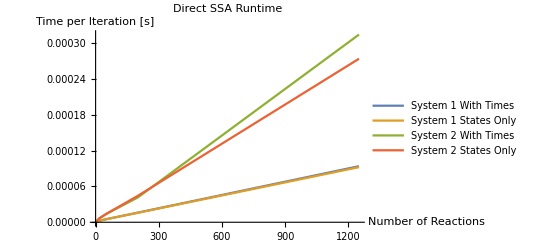

```mathematica
coorsSSA2=Flatten[Table[
Table[{resultsSSA2[[i]][[j]][[l]][[3]],resultsSSA2[[i]][[j]][[l]][[7]]},{l,Length[resultsSSA2[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1","System 2"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA2,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA2.mx"},OperatingSystem->$OperatingSystem], resultsSSA2];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA2.mx"},OperatingSystem->$OperatingSystem], coorsSSA2];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA2=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA2.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA2=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA2.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.109375,1.04655×10^-6,<|frontend→0.015625,interface→6.9×10^-6,backend→0.104655|>},{ConstructSys1,False,18,18,100000,0.25,2.50539×10^-6,<|frontend→0.,interface→0.0000224,backend→0.250539|>},{ConstructSys1,False,50,50,100000,0.5,5.03736×10^-6,<|frontend→0.,interface→0.0000828,backend→0.503736|>},{ConstructSys1,False,200,200,100000,1.64063,0.0000160502,<|frontend→0.046875,interface→0.000303,backend→1.60502|>},{ConstructSys1,False,1250,1250,100000,9.71875,0.0000937455,<|frontend→0.359375,interface→0.0021664,backend→9.37455|>}},{{ConstructSys1,True,2,2,100000,0.109375,1.08565×10^-6,<|frontend→0.,interface→6.9×10^-6,backend→0.108565|>},{ConstructSys1,True,18,18,100000,0.234375,2.40364×10^-6,<|frontend→0.,interface→0.0000215,backend→0.240364|>},{ConstructSys1,True,50,50,100000,0.5,5.1094×10^-6,<|frontend→0.,interface→0.0000691,backend→0.51094|>},{ConstructSys1,True,200,200,100000,1.60938,0.0000157617,<|frontend→0.03125,interface→0.000146,backend→1.57617|>},{ConstructSys1,True,1250,1250,100000,9.57813,0.000092176,<|frontend→0.359375,interface→0.0024062,backend→9.2176|>}}},{{{ConstructSys2,False,2,2,100000,0.125,1.14791×10^-6,<|frontend→0.,interface→5.9×10^-6,backend→0.114791|>},{ConstructSys2,False,18,18,100000,0.671875,6.67445×10^-6,<|frontend→0.,interface→0.0000487,backend→0.667445|>},{ConstructSys2,False,50,50,100000,1.375,0.0000136453,<|frontend→0.015625,interface→0.00017,backend→1.36453|>},{ConstructSys2,False,200,200,100000,4.21875,0.0000413932,<|frontend→0.0625,interface→0.0003924,backend→4.13932|>},{ConstructSys2,False,1250,1250,100000,32.,0.000313927,<|frontend→1.,interface→0.0071793,backend→31.3927|>}},{{ConstructSys2,True,2,2,100000,0.140625,1.01557×10^-6,<|frontend→0.03125,interface→9.×10^-6,backend→0.101557|>},{ConstructSys2,True,18,18,100000,0.65625,6.5635×10^-6,<|frontend→0.,interface→0.0000336,backend→0.65635|>},{ConstructSys2,True,50,50,100000,1.375,0.0000139442,<|frontend→0.015625,interface→0.0002032,backend→1.39442|>},{ConstructSys2,True,200,200,100000,4.48438,0.0000440932,<|frontend→0.0625,interface→0.0004626,backend→4.40932|>},{ConstructSys2,True,1250,1250,100000,27.875,0.000273477,<|frontend→1.01563,interface→0.0062821,backend→27.3477|>}}}}

{{{2,1.04655×10^-6},{18,2.50539×10^-6},{50,5.03736×10^-6},{200,0.0000160502},{1250,0.0000937455}},{{2,1.08565×10^-6},{18,2.40364×10^-6},{50,5.1094×10^-6},{200,0.0000157617},{1250,0.000092176}},{{2,1.14791×10^-6},{18,6.67445×10^-6},{50,0.0000136453},{200,0.0000413932},{1250,0.000313927}},{{2,1.01557×10^-6},{18,6.5635×10^-6},{50,0.0000139442},{200,0.0000440932},{1250,0.000273477}}}

## Construction 1 up to 20,000 reactions

```mathematica
constructions={ConstructSys1};
kRange={1,3,5,10,25,50,100};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA3=Table[TestSysSSA[constructions[[i]],kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.109375,9.86808×10^-7,<|frontend→0.,interface→0.000015,backend→0.0986808|>}

{ConstructSys1,False,18,18,100000,0.21875,2.20835×10^-6,<|frontend→0.,interface→0.0000203,backend→0.220835|>}

{ConstructSys1,False,50,50,100000,0.5,4.93301×10^-6,<|frontend→0.,interface→0.0000423,backend→0.493301|>}

{ConstructSys1,False,200,200,100000,1.54688,0.0000152985,<|frontend→0.03125,interface→0.0002426,backend→1.52985|>}

{ConstructSys1,False,1250,1250,100000,9.73438,0.0000946454,<|frontend→0.3125,interface→0.0049099,backend→9.46454|>}

{ConstructSys1,False,5000,5000,100000,42.3438,0.000379971,<|frontend→4.29688,interface→0.0421701,backend→37.9971|>}

{ConstructSys1,False,20000,20000,100000,242.438,0.00174344,<|frontend→67.0313,interface→0.854242,backend→174.344|>}

{ConstructSys1,True,2,2,100000,0.15625,1.25702×10^-6,<|frontend→0.03125,interface→8.3×10^-6,backend→0.125702|>}

{ConstructSys1,True,18,18,100000,0.28125,2.99453×10^-6,<|frontend→0.,interface→0.0000306,backend→0.299453|>}

{ConstructSys1,True,50,50,100000,0.53125,5.12735×10^-6,<|frontend→0.015625,interface→0.0006015,backend→0.512735|>}

{ConstructSys1,True,200,200,100000,1.625,0.0000159824,<|frontend→0.03125,interface→0.0004841,backend→1.59824|>}

{ConstructSys1,True,1250,1250,100000,9.67188,0.0000934454,<|frontend→0.359375,interface→0.0023943,backend→9.34454|>}

{ConstructSys1,True,5000,5000,100000,48.1875,0.00043805,<|frontend→4.35938,interface→0.040135,backend→43.805|>}

{ConstructSys1,True,20000,20000,100000,240.047,0.00173151,<|frontend→64.3906,interface→0.710312,backend→173.151|>}

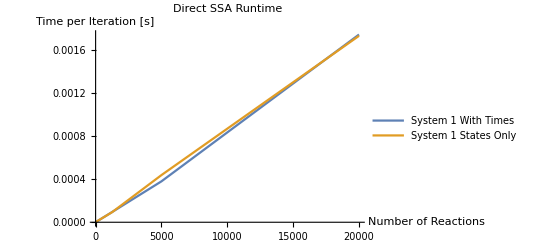

```mathematica
coorsSSA3=Flatten[Table[
Table[{resultsSSA3[[i]][[j]][[l]][[3]],resultsSSA3[[i]][[j]][[l]][[7]]},{l,Length[resultsSSA3[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA3,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA3.mx"},OperatingSystem->$OperatingSystem], resultsSSA3];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA3.mx"},OperatingSystem->$OperatingSystem], coorsSSA3];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA3=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA3.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA3=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA3.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.109375,9.86808×10^-7,<|frontend→0.,interface→0.000015,backend→0.0986808|>},{ConstructSys1,False,18,18,100000,0.21875,2.20835×10^-6,<|frontend→0.,interface→0.0000203,backend→0.220835|>},{ConstructSys1,False,50,50,100000,0.5,4.93301×10^-6,<|frontend→0.,interface→0.0000423,backend→0.493301|>},{ConstructSys1,False,200,200,100000,1.54688,0.0000152985,<|frontend→0.03125,interface→0.0002426,backend→1.52985|>},{ConstructSys1,False,1250,1250,100000,9.73438,0.0000946454,<|frontend→0.3125,interface→0.0049099,backend→9.46454|>},{ConstructSys1,False,5000,5000,100000,42.3438,0.000379971,<|frontend→4.29688,interface→0.0421701,backend→37.9971|>},{ConstructSys1,False,20000,20000,100000,242.438,0.00174344,<|frontend→67.0313,interface→0.854242,backend→174.344|>}},{{ConstructSys1,True,2,2,100000,0.15625,1.25702×10^-6,<|frontend→0.03125,interface→8.3×10^-6,backend→0.125702|>},{ConstructSys1,True,18,18,100000,0.28125,2.99453×10^-6,<|frontend→0.,interface→0.0000306,backend→0.299453|>},{ConstructSys1,True,50,50,100000,0.53125,5.12735×10^-6,<|frontend→0.015625,interface→0.0006015,backend→0.512735|>},{ConstructSys1,True,200,200,100000,1.625,0.0000159824,<|frontend→0.03125,interface→0.0004841,backend→1.59824|>},{ConstructSys1,True,1250,1250,100000,9.67188,0.0000934454,<|frontend→0.359375,interface→0.0023943,backend→9.34454|>},{ConstructSys1,True,5000,5000,100000,48.1875,0.00043805,<|frontend→4.35938,interface→0.040135,backend→43.805|>},{ConstructSys1,True,20000,20000,100000,240.047,0.00173151,<|frontend→64.3906,interface→0.710312,backend→173.151|>}}}}

{{{2,9.86808×10^-7},{18,2.20835×10^-6},{50,4.93301×10^-6},{200,0.0000152985},{1250,0.0000946454},{5000,0.000379971},{20000,0.00174344}},{{2,1.25702×10^-6},{18,2.99453×10^-6},{50,5.12735×10^-6},{200,0.0000159824},{1250,0.0000934454},{5000,0.00043805},{20000,0.00173151}}}

## Bounded Tau Leaping

```mathematica
<<StoChemSim`
```

```mathematica
ConstructSysMax[n_]:={
rxnl[{x1},{y,z1},1],
rxnl[{x2},{y,z2},1],
rxnl[{z1,z2},{k},1/n],
rxnl[{k,y},{},1/n],
conc[{x1,x2},n/2]
};
```

```mathematica
TestSysBTL[construction_,simulation_,nRange_]:=Module[{},
Table[Module[
{rxnsys,results,totalTime,runtimeInfo,algoTime},
rxnsys= construction[n];
results=Timing[simulation[rxnsys,finalOnly->True,outputTS->False]];
totalTime=results[[1]];
runtimeInfo=GetRuntimeInfo[];
out={simulation,n,totalTime,runtimeInfo};
Print[out];
out],
{n,nRange}]]
```

## Direct SSA vs. BTL up to 32,768 molecules

```mathematica
simulations={SimulateDirectSSA,SimulateBoundedTauLeaping};
nRange=Table[2^i,{i,1,15}];
resultsBTL=Table[TestSysBTL[ConstructSysMax,simulations[[i]],nRange],{i,Length[simulations]}];
```

{SimulateDirectSSA,2,0.015625,<|frontend→0.015625,interface→0.000016,backend→0.0012471|>}

{SimulateDirectSSA,4,0.,<|frontend→0.,interface→9.7×10^-6,backend→0.0004594|>}

{SimulateDirectSSA,8,0.,<|frontend→0.,interface→5.8×10^-6,backend→0.000866|>}

{SimulateDirectSSA,16,0.,<|frontend→0.,interface→5.1×10^-6,backend→0.0000602|>}

{SimulateDirectSSA,32,0.,<|frontend→0.,interface→4.7×10^-6,backend→0.0001293|>}

{SimulateDirectSSA,64,0.015625,<|frontend→0.,interface→6.8×10^-6,backend→0.0001623|>}

{SimulateDirectSSA,128,0.,<|frontend→0.,interface→8.8×10^-6,backend→0.0004091|>}

{SimulateDirectSSA,256,0.,<|frontend→0.,interface→5.4×10^-6,backend→0.0006556|>}

{SimulateDirectSSA,512,0.,<|frontend→0.,interface→5.5×10^-6,backend→0.0013157|>}

{SimulateDirectSSA,1024,0.,<|frontend→0.,interface→7.8×10^-6,backend→0.004772|>}

{SimulateDirectSSA,2048,0.015625,<|frontend→0.,interface→6.2×10^-6,backend→0.0057106|>}

{SimulateDirectSSA,4096,0.,<|frontend→0.,interface→7.8×10^-6,backend→0.0113347|>}

{SimulateDirectSSA,8192,0.03125,<|frontend→0.,interface→8.1×10^-6,backend→0.0216833|>}

{SimulateDirectSSA,16384,0.046875,<|frontend→0.,interface→0.0000183,backend→0.0440275|>}

{SimulateDirectSSA,32768,0.078125,<|frontend→0.,interface→6.1×10^-6,backend→0.0878965|>}

{SimulateBoundedTauLeaping,2,0.,<|frontend→0.,interface→6.6×10^-6,backend→0.0009589|>}

{SimulateBoundedTauLeaping,4,0.,<|frontend→0.,interface→7.5×10^-6,backend→0.0001275|>}

{SimulateBoundedTauLeaping,8,0.,<|frontend→0.,interface→7.2×10^-6,backend→0.0002533|>}

{SimulateBoundedTauLeaping,16,0.,<|frontend→0.,interface→0.0000289,backend→0.0006843|>}

{SimulateBoundedTauLeaping,32,0.,<|frontend→0.,interface→8.5×10^-6,backend→0.000947|>}

{SimulateBoundedTauLeaping,64,0.,<|frontend→0.,interface→7.2×10^-6,backend→0.0019396|>}

{SimulateBoundedTauLeaping,128,0.,<|frontend→0.,interface→7.5×10^-6,backend→0.0036934|>}

{SimulateBoundedTauLeaping,256,0.015625,<|frontend→0.,interface→7.1×10^-6,backend→0.0076757|>}

{SimulateBoundedTauLeaping,512,0.015625,<|frontend→0.,interface→5.5×10^-6,backend→0.0114099|>}

{SimulateBoundedTauLeaping,1024,0.015625,<|frontend→0.,interface→5.7×10^-6,backend→0.0170177|>}

{SimulateBoundedTauLeaping,2048,0.015625,<|frontend→0.,interface→9.5×10^-6,backend→0.0232597|>}

{SimulateBoundedTauLeaping,4096,0.03125,<|frontend→0.,interface→5.6×10^-6,backend→0.0292565|>}

{SimulateBoundedTauLeaping,8192,0.03125,<|frontend→0.,interface→8.2×10^-6,backend→0.0336564|>}

{SimulateBoundedTauLeaping,16384,0.0625,<|frontend→0.,interface→6.1×10^-6,backend→0.0488705|>}

{SimulateBoundedTauLeaping,32768,0.0625,<|frontend→0.,interface→5.9×10^-6,backend→0.0683247|>}

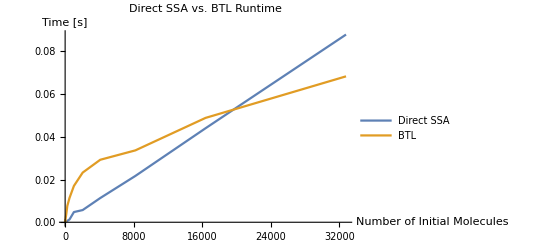

```mathematica
coorsBTL=Table[
Table[{resultsBTL[[i]][[l]][[2]],resultsBTL[[i]][[l]][[4]]["backend"]},{l,Length[resultsBTL[[i]]]}],
{i,Length[simulations]}];
simulationLabels={"Direct SSA","BTL"};
ListLinePlot[
coorsBTL,
PlotLegends->simulationLabels,
AxesLabel->{"Number of Initial Molecules","Time [s]"},
PlotLabel->"Direct SSA vs. BTL Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL.mx"},OperatingSystem->$OperatingSystem], resultsBTL];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL.mx"},OperatingSystem->$OperatingSystem], coorsBTL];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsBTL=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL.mx"},OperatingSystem->$OperatingSystem]]
coorsBTL=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL.mx"},OperatingSystem->$OperatingSystem]]
```

{{{SimulateDirectSSA,2,0.015625,<|frontend→0.015625,interface→0.000016,backend→0.0012471|>},{SimulateDirectSSA,4,0.,<|frontend→0.,interface→9.7×10^-6,backend→0.0004594|>},{SimulateDirectSSA,8,0.,<|frontend→0.,interface→5.8×10^-6,backend→0.000866|>},{SimulateDirectSSA,16,0.,<|frontend→0.,interface→5.1×10^-6,backend→0.0000602|>},{SimulateDirectSSA,32,0.,<|frontend→0.,interface→4.7×10^-6,backend→0.0001293|>},{SimulateDirectSSA,64,0.015625,<|frontend→0.,interface→6.8×10^-6,backend→0.0001623|>},{SimulateDirectSSA,128,0.,<|frontend→0.,interface→8.8×10^-6,backend→0.0004091|>},{SimulateDirectSSA,256,0.,<|frontend→0.,interface→5.4×10^-6,backend→0.0006556|>},{SimulateDirectSSA,512,0.,<|frontend→0.,interface→5.5×10^-6,backend→0.0013157|>},{SimulateDirectSSA,1024,0.,<|frontend→0.,interface→7.8×10^-6,backend→0.004772|>},{SimulateDirectSSA,2048,0.015625,<|frontend→0.,interface→6.2×10^-6,backend→0.0057106|>},{SimulateDirectSSA,4096,0.,<|frontend→0.,interface→7.8×10^-6,backend→0.0113347|>},{SimulateDirectSSA,8192,0.03125,<|frontend→0.,interface→8.1×10^-6,backend→0.0216833|>},{SimulateDirectSSA,16384,0.046875,<|frontend→0.,interface→0.0000183,backend→0.0440275|>},{SimulateDirectSSA,32768,0.078125,<|frontend→0.,interface→6.1×10^-6,backend→0.0878965|>}},{{SimulateBoundedTauLeaping,2,0.,<|frontend→0.,interface→6.6×10^-6,backend→0.0009589|>},{SimulateBoundedTauLeaping,4,0.,<|frontend→0.,interface→7.5×10^-6,backend→0.0001275|>},{SimulateBoundedTauLeaping,8,0.,<|frontend→0.,interface→7.2×10^-6,backend→0.0002533|>},{SimulateBoundedTauLeaping,16,0.,<|frontend→0.,interface→0.0000289,backend→0.0006843|>},{SimulateBoundedTauLeaping,32,0.,<|frontend→0.,interface→8.5×10^-6,backend→0.000947|>},{SimulateBoundedTauLeaping,64,0.,<|frontend→0.,interface→7.2×10^-6,backend→0.0019396|>},{SimulateBoundedTauLeaping,128,0.,<|frontend→0.,interface→7.5×10^-6,backend→0.0036934|>},{SimulateBoundedTauLeaping,256,0.015625,<|frontend→0.,interface→7.1×10^-6,backend→0.0076757|>},{SimulateBoundedTauLeaping,512,0.015625,<|frontend→0.,interface→5.5×10^-6,backend→0.0114099|>},{SimulateBoundedTauLeaping,1024,0.015625,<|frontend→0.,interface→5.7×10^-6,backend→0.0170177|>},{SimulateBoundedTauLeaping,2048,0.015625,<|frontend→0.,interface→9.5×10^-6,backend→0.0232597|>},{SimulateBoundedTauLeaping,4096,0.03125,<|frontend→0.,interface→5.6×10^-6,backend→0.0292565|>},{SimulateBoundedTauLeaping,8192,0.03125,<|frontend→0.,interface→8.2×10^-6,backend→0.0336564|>},{SimulateBoundedTauLeaping,16384,0.0625,<|frontend→0.,interface→6.1×10^-6,backend→0.0488705|>},{SimulateBoundedTauLeaping,32768,0.0625,<|frontend→0.,interface→5.9×10^-6,backend→0.0683247|>}}}

{{{2,0.0012471},{4,0.0004594},{8,0.000866},{16,0.0000602},{32,0.0001293},{64,0.0001623},{128,0.0004091},{256,0.0006556},{512,0.0013157},{1024,0.004772},{2048,0.0057106},{4096,0.0113347},{8192,0.0216833},{16384,0.0440275},{32768,0.0878965}},{{2,0.0009589},{4,0.0001275},{8,0.0002533},{16,0.0006843},{32,0.000947},{64,0.0019396},{128,0.0036934},{256,0.0076757},{512,0.0114099},{1024,0.0170177},{2048,0.0232597},{4096,0.0292565},{8192,0.0336564},{16384,0.0488705},{32768,0.0683247}}}

## Direct SSA vs. BTL up to 1,000,000 molecules

```mathematica
simulations={SimulateDirectSSA,SimulateBoundedTauLeaping};
nRange=Table[10^i,{i,1,6}];
resultsBTL2=Table[TestSysBTL[ConstructSysMax,simulations[[i]],nRange],{i,Length[simulations]}];
```

{SimulateDirectSSA,10,0.,<|frontend→0.,interface→8.4×10^-6,backend→0.0001028|>}

{SimulateDirectSSA,100,0.,<|frontend→0.,interface→4.9×10^-6,backend→0.0002795|>}

{SimulateDirectSSA,1000,0.,<|frontend→0.,interface→4.8×10^-6,backend→0.0024228|>}

{SimulateDirectSSA,10000,0.03125,<|frontend→0.,interface→6.9×10^-6,backend→0.0315906|>}

{SimulateDirectSSA,100000,0.265625,<|frontend→0.,interface→8.6×10^-6,backend→0.25897|>}

{SimulateDirectSSA,1000000,2.39063,<|frontend→0.,interface→9.9×10^-6,backend→2.41952|>}

{SimulateBoundedTauLeaping,10,0.,<|frontend→0.,interface→5.5×10^-6,backend→0.000269|>}

{SimulateBoundedTauLeaping,100,0.,<|frontend→0.,interface→5.5×10^-6,backend→0.0027333|>}

{SimulateBoundedTauLeaping,1000,0.015625,<|frontend→0.,interface→6.9×10^-6,backend→0.016234|>}

{SimulateBoundedTauLeaping,10000,0.046875,<|frontend→0.,interface→5.7×10^-6,backend→0.035583|>}

{SimulateBoundedTauLeaping,100000,0.09375,<|frontend→0.,interface→8.7×10^-6,backend→0.0891383|>}

{SimulateBoundedTauLeaping,1000000,0.234375,<|frontend→0.,interface→7.×10^-6,backend→0.246433|>}

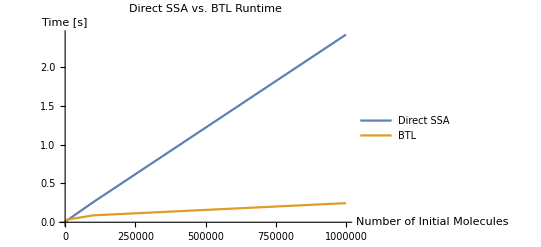

```mathematica
coorsBTL2=Table[
Table[{resultsBTL2[[i]][[l]][[2]],resultsBTL2[[i]][[l]][[4]]["backend"]},{l,Length[resultsBTL2[[i]]]}],
{i,Length[simulations]}];
simulationLabels={"Direct SSA","BTL"};
ListLinePlot[
coorsBTL2,
PlotLegends->simulationLabels,
AxesLabel->{"Number of Initial Molecules","Time [s]"},
PlotLabel->"Direct SSA vs. BTL Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL2.mx"},OperatingSystem->$OperatingSystem], resultsBTL2];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL2.mx"},OperatingSystem->$OperatingSystem], coorsBTL2];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsBTL2=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL2.mx"},OperatingSystem->$OperatingSystem]]
coorsBTL2=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL2.mx"},OperatingSystem->$OperatingSystem]]
```

{{{SimulateDirectSSA,10,0.,<|frontend→0.,interface→8.4×10^-6,backend→0.0001028|>},{SimulateDirectSSA,100,0.,<|frontend→0.,interface→4.9×10^-6,backend→0.0002795|>},{SimulateDirectSSA,1000,0.,<|frontend→0.,interface→4.8×10^-6,backend→0.0024228|>},{SimulateDirectSSA,10000,0.03125,<|frontend→0.,interface→6.9×10^-6,backend→0.0315906|>},{SimulateDirectSSA,100000,0.265625,<|frontend→0.,interface→8.6×10^-6,backend→0.25897|>},{SimulateDirectSSA,1000000,2.39063,<|frontend→0.,interface→9.9×10^-6,backend→2.41952|>}},{{SimulateBoundedTauLeaping,10,0.,<|frontend→0.,interface→5.5×10^-6,backend→0.000269|>},{SimulateBoundedTauLeaping,100,0.,<|frontend→0.,interface→5.5×10^-6,backend→0.0027333|>},{SimulateBoundedTauLeaping,1000,0.015625,<|frontend→0.,interface→6.9×10^-6,backend→0.016234|>},{SimulateBoundedTauLeaping,10000,0.046875,<|frontend→0.,interface→5.7×10^-6,backend→0.035583|>},{SimulateBoundedTauLeaping,100000,0.09375,<|frontend→0.,interface→8.7×10^-6,backend→0.0891383|>},{SimulateBoundedTauLeaping,1000000,0.234375,<|frontend→0.,interface→7.×10^-6,backend→0.246433|>}}}

{{{10,0.0001028},{100,0.0002795},{1000,0.0024228},{10000,0.0315906},{100000,0.25897},{1000000,2.41952}},{{10,0.000269},{100,0.0027333},{1000,0.016234},{10000,0.035583},{100000,0.0891383},{1000000,0.246433}}}